# Higgs to digluon SM vs MSSM test

## Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
<<FeynArts`
<<FormCalc`
```

FeynArts 3.10 (11 Jul 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.6 (16 Apr 2018)

by Thomas Hahn

## Diagram Creation

> Top. 1 ad/becf/dedfef.m, 1 diagram

> Top. 2 ad/bece/dede.m, 1 diagram

> Top. 3 ad/becd/eded.m, 1 diagram

> Top. 4 ad/bdce/eded.m, 1 diagram

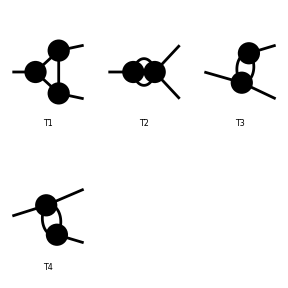

```mathematica
topo1=CreateTopologies[1,1->2,ExcludeTopologies->{Internal}];
Paint[topo1];
```

Excluding 0 Generic, 27 Classes, and 64 Particles fields

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 6 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 0 Generic, 27 Classes, and 64 Particles fields

Restoring 18 field point(s)

in total: 8 Particles insertions

> Top. 1 ad/becf/dedfef.m, 6 diagrams

> Top. 2 ad/bece/dede.m, 2 diagrams

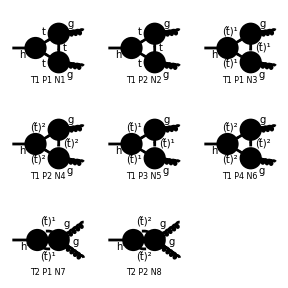

```mathematica
diag1=InsertFields[topo1,{S[1]}->{V[5],V[5]},InsertionLevel->{Particles},Model->"MSSMQCD",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[2],S[11],S[12],S[13,{1,1}],S[13,{2,1}],S[13,{1,2}],S[13,{2,2}],(*S[13,{1,3}],S[13,{2,3}],*)S[14],S[4],S[5],S[6],F[11],F[12],U[1],U[2],U[3],U[4]},Restrictions->NoLightFHCoupling];
Paint[diag1];
```

## Generate Amplitude

```mathematica
ClearProcess[];
amp=CalcFeynAmp[(*OffShell[*)CreateFeynAmp[diag1](*,2-> mg1,3-> mg2]*),FermionChains->Chiral]//Simplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 6 Particles amplitudes

> Top. 2: 2 Particles amplitudes

in total: 8 Particles amplitudes

preparing FORM code in /home/paul/projects/physics/Research/Tests/fc-amp-1.frm

running FORM...

ok

Amp[{{S[1],k[1],Mh0,{}}}→{{V[5,{Glu2}],k[2],0,{√3 ColorCharge}},{V[5,{Glu3}],k[3],0,{√3 ColorCharge}}}][1/(3 CW MW π SB SW)Alfas EL (1/4 Pair1 (12 CA CW MT2 B0i[bb0,0,MT2,MT2]-Sub51 B0i[bb0,Mh02,MSf2[1,3,3],MSf2[1,3,3]]-Sub91 B0i[bb0,Mh02,MSf2[2,3,3],MSf2[2,3,3]]+4 Sub51 C0i[cc00,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+4 Sub91 C0i[cc00,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]])-3 CA CW MT2 (1/2 Abb1 C0i[cc0,0,0,Mh02,MT2,MT2,MT2]+4 Pair1 C0i[cc00,0,0,Mh02,MT2,MT2,MT2]+Abb2 C0i[cc2,0,0,Mh02,MT2,MT2,MT2]+4 Pair2 Pair3 (C0i[cc12,0,0,Mh02,MT2,MT2,MT2]+C0i[cc22,0,0,Mh02,MT2,MT2,MT2]))+Pair2 Pair3 (Sub51 (C0i[cc12,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc2,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc22,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]])+Sub91 (C0i[cc12,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]+C0i[cc2,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]+C0i[cc22,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]))) Mat[SUN1]]

#### Check divergent piece

```mathematica
uvcheck=UVDivergentPart[expr]//Simplify;
FreeQ[uvcheck,Divergence]
```

True

```mathematica
UVDivergentPart[amp]//Simplify
divergence=%[[1]]
```

Amp[{{S[1],k[1],Mh0,{}}}→{{V[5,{Glu2}],k[2],0,{√3 ColorCharge}},{V[5,{Glu3}],k[3],0,{√3 ColorCharge}}}][0]

0

#### Prepare for looptools

```mathematica
squ=SquaredME[amp];
(* If contains Fermion *)
(*** Don't forget to multiply for FINAL fermions. ***)
squ=(1(squ[[1]]//.squ[[2]]))//.HelicityME[amp]//.{Hel[_]->0}; (* or simply with _Hel=0 *)
(* If contains Colored Particles *)
(*** Don't forget to divide for INITIAL colored particles. ***)

squ=(squ//.ColourME[amp])/1;
(* If contains Vector *)
(*** Don't forget to divide for initial vectors. ***)

mat= PolarizationSum[squ,GaugeTerms->False]/1;  (*Asserting gauge invariance! *)
```

HelicityME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /home/paul/projects/physics/Research/Tests/fc-pol-1.frm

running FORM...

ok

Note: polarization sum auto squares the matrix element. Subexpr seems to destroy this line.

```mathematica
(*mat=PolarizationSum[amp,GaugeTerms->False]//.Subexpr[]//.Abbr[]//Simplify*)
```

# Input point

## Inputs

```mathematica
stopM1 = 25000;
stopM2 = 10000;
mixT = 0;
muM = 250;
betaA = 1.47; (*tan beta = 10*)
alphaA = betaA - (Pi/2);
offM1 =0.0001;
offM2 = 0.0001;
Clear[matSq,c1,c2,ghSS,h11,h12,h22,z11,z12,z22,m,mh,mZ,mW]
```

# FeynArts Evaluation

## Numerical Evaluation

```mathematica
matPostSub = mat//.Subexpr[]//. mg1 -> offM1 //.mg2-> offM2
```

1/(9 CW2 MW2 π SB2 SW2)Alfa Alfas2 (36 CA2 CW2 Mh02^2 MT2^2 (C0i[cc0,0,0,Mh02,MT2,MT2,MT2]+4 (C0i[cc12,0,0,Mh02,MT2,MT2,MT2]+C0i[cc2,0,0,Mh02,MT2,MT2,MT2]+C0i[cc22,0,0,Mh02,MT2,MT2,MT2])) C0i[cc0,0,0,Mh02,MT2,MT2,MT2]^*-48 C0i[cc00,0,0,Mh02,MT2,MT2,MT2]^* (-12 CA2 CW2 MT2^2 (4 C0i[cc00,0,0,Mh02,MT2,MT2,MT2]+Mh02 (C0i[cc2,0,0,Mh02,MT2,MT2,MT2]+2 (C0i[cc12,0,0,Mh02,MT2,MT2,MT2]+C0i[cc22,0,0,Mh02,MT2,MT2,MT2])))+CA CW MT2 (12 CA CW MT2 B0i[bb0,0,MT2,MT2]-(B0i[bb0,Mh02,MSf2[1,3,3],MSf2[1,3,3]]-4 C0i[cc00,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]) (((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USf[1,1,3,3]+3 CW MT (MUEC SA+CA Af[3,3,3]) USf[1,2,3,3]) USfC[1,1,3,3]+(-4 MW MZ SAB SB SW2 USf[1,2,3,3]+3 CW (MT (MUE SA+CA AfC[3,3,3]) USf[1,1,3,3]+2 CA MT2 USf[1,2,3,3])) USfC[1,2,3,3])-(B0i[bb0,Mh02,MSf2[2,3,3],MSf2[2,3,3]]-4 C0i[cc00,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]) (((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USf[2,1,3,3]+3 CW MT (MUEC SA+CA Af[3,3,3]) USf[2,2,3,3]) USfC[2,1,3,3]+(-4 MW MZ SAB SB SW2 USf[2,2,3,3]+3 CW (MT (MUE SA+CA AfC[3,3,3]) USf[2,1,3,3]+2 CA MT2 USf[2,2,3,3])) USfC[2,2,3,3])+2 Mh02 ((C0i[cc12,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc2,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc22,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]) (((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USf[1,1,3,3]+3 CW MT (MUEC SA+CA Af[3,3,3]) USf[1,2,3,3]) USfC[1,1,3,3]+(-4 MW MZ SAB SB SW2 USf[1,2,3,3]+3 CW (MT (MUE SA+CA AfC[3,3,3]) USf[1,1,3,3]+2 CA MT2 USf[1,2,3,3])) USfC[1,2,3,3])+(C0i[cc12,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]+C0i[cc2,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]+C0i[cc22,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]) (((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USf[2,1,3,3]+3 CW MT (MUEC SA+CA Af[3,3,3]) USf[2,2,3,3]) USfC[2,1,3,3]+(-4 MW MZ SAB SB SW2 USf[2,2,3,3]+3 CW (MT (MUE SA+CA AfC[3,3,3]) USf[2,1,3,3]+2 CA MT2 USf[2,2,3,3])) USfC[2,2,3,3]))))-24 (C0i[cc12,0,0,Mh02,MT2,MT2,MT2]^*+C0i[cc22,0,0,Mh02,MT2,MT2,MT2]^*) (-6 CA2 CW2 MT2^2 (8 (Mh02 C0i[cc00,0,0,Mh02,MT2,MT2,MT2]+Mh02^2 C0i[cc12,0,0,Mh02,MT2,MT2,MT2])+Mh02^2 (C0i[cc0,0,0,Mh02,MT2,MT2,MT2]+6 C0i[cc2,0,0,Mh02,MT2,MT2,MT2]+8 C0i[cc22,0,0,Mh02,MT2,MT2,MT2]))+CA CW MT2 (-Mh02 (-12 CA CW MT2 B0i[bb0,0,MT2,MT2]+(B0i[bb0,Mh02,MSf2[1,3,3],MSf2[1,3,3]]-4 C0i[cc00,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]) (((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USf[1,1,3,3]+3 CW MT (MUEC SA+CA Af[3,3,3]) USf[1,2,3,3]) USfC[1,1,3,3]+(-4 MW MZ SAB SB SW2 USf[1,2,3,3]+3 CW (MT (MUE SA+CA AfC[3,3,3]) USf[1,1,3,3]+2 CA MT2 USf[1,2,3,3])) USfC[1,2,3,3])+(B0i[bb0,Mh02,MSf2[2,3,3],MSf2[2,3,3]]-4 C0i[cc00,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]) (((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USf[2,1,3,3]+3 CW MT (MUEC SA+CA Af[3,3,3]) USf[2,2,3,3]) USfC[2,1,3,3]+(-4 MW MZ SAB SB SW2 USf[2,2,3,3]+3 CW (MT (MUE SA+CA AfC[3,3,3]) USf[2,1,3,3]+2 CA MT2 USf[2,2,3,3])) USfC[2,2,3,3]))+4 Mh02^2 ((C0i[cc12,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc2,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc22,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]) (((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USf[1,1,3,3]+3 CW MT (MUEC SA+CA Af[3,3,3]) USf[1,2,3,3]) USfC[1,1,3,3]+(-4 MW MZ SAB SB SW2 USf[1,2,3,3]+3 CW (MT (MUE SA+CA AfC[3,3,3]) USf[1,1,3,3]+2 CA MT2 USf[1,2,3,3])) USfC[1,2,3,3])+(C0i[cc12,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]+C0i[cc2,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]+C0i[cc22,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]) (((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USf[2,1,3,3]+3 CW MT (MUEC SA+CA Af[3,3,3]) USf[2,2,3,3]) USfC[2,1,3,3]+(-4 MW MZ SAB SB SW2 USf[2,2,3,3]+3 CW (MT (MUE SA+CA AfC[3,3,3]) USf[2,1,3,3]+2 CA MT2 USf[2,2,3,3])) USfC[2,2,3,3]))))-12 C0i[cc2,0,0,Mh02,MT2,MT2,MT2]^* (-12 CA2 CW2 MT2^2 (4 Mh02 C0i[cc00,0,0,Mh02,MT2,MT2,MT2]+Mh02^2 (C0i[cc0,0,0,Mh02,MT2,MT2,MT2]+5 C0i[cc2,0,0,Mh02,MT2,MT2,MT2]+6 (C0i[cc12,0,0,Mh02,MT2,MT2,MT2]+C0i[cc22,0,0,Mh02,MT2,MT2,MT2])))+CA CW MT2 (-Mh02 (-12 CA CW MT2 B0i[bb0,0,MT2,MT2]+(B0i[bb0,Mh02,MSf2[1,3,3],MSf2[1,3,3]]-4 C0i[cc00,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]) (((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USf[1,1,3,3]+3 CW MT (MUEC SA+CA Af[3,3,3]) USf[1,2,3,3]) USfC[1,1,3,3]+(-4 MW MZ SAB SB SW2 USf[1,2,3,3]+3 CW (MT (MUE SA+CA AfC[3,3,3]) USf[1,1,3,3]+2 CA MT2 USf[1,2,3,3])) USfC[1,2,3,3])+(B0i[bb0,Mh02,MSf2[2,3,3],MSf2[2,3,3]]-4 C0i[cc00,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]) (((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USf[2,1,3,3]+3 CW MT (MUEC SA+CA Af[3,3,3]) USf[2,2,3,3]) USfC[2,1,3,3]+(-4 MW MZ SAB SB SW2 USf[2,2,3,3]+3 CW (MT (MUE SA+CA AfC[3,3,3]) USf[2,1,3,3]+2 CA MT2 USf[2,2,3,3])) USfC[2,2,3,3]))+6 Mh02^2 ((C0i[cc12,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc2,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc22,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]) (((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USf[1,1,3,3]+3 CW MT (MUEC SA+CA Af[3,3,3]) USf[1,2,3,3]) USfC[1,1,3,3]+(-4 MW MZ SAB SB SW2 USf[1,2,3,3]+3 CW (MT (MUE SA+CA AfC[3,3,3]) USf[1,1,3,3]+2 CA MT2 USf[1,2,3,3])) USfC[1,2,3,3])+(C0i[cc12,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]+C0i[cc2,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]+C0i[cc22,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]) (((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USf[2,1,3,3]+3 CW MT (MUEC SA+CA Af[3,3,3]) USf[2,2,3,3]) USfC[2,1,3,3]+(-4 MW MZ SAB SB SW2 USf[2,2,3,3]+3 CW (MT (MUE SA+CA AfC[3,3,3]) USf[2,1,3,3]+2 CA MT2 USf[2,2,3,3])) USfC[2,2,3,3]))))+(-12 CA CW MT2 B0i[bb0,0,MT2,MT2]+(B0i[bb0,Mh02,MSf2[1,3,3],MSf2[1,3,3]]-4 C0i[cc00,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]) (((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USf[1,1,3,3]+3 CW MT (MUEC SA+CA Af[3,3,3]) USf[1,2,3,3]) USfC[1,1,3,3]+(-4 MW MZ SAB SB SW2 USf[1,2,3,3]+3 CW (MT (MUE SA+CA AfC[3,3,3]) USf[1,1,3,3]+2 CA MT2 USf[1,2,3,3])) USfC[1,2,3,3])+(B0i[bb0,Mh02,MSf2[2,3,3],MSf2[2,3,3]]-4 C0i[cc00,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]) (((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USf[2,1,3,3]+3 CW MT (MUEC SA+CA Af[3,3,3]) USf[2,2,3,3]) USfC[2,1,3,3]+(-4 MW MZ SAB SB SW2 USf[2,2,3,3]+3 CW (MT (MUE SA+CA AfC[3,3,3]) USf[2,1,3,3]+2 CA MT2 USf[2,2,3,3])) USfC[2,2,3,3])) (-12 CA CW MT2 B0i[bb0,0,MT2,MT2]^*+(B0i[bb0,Mh02,MSf2[1,3,3],MSf2[1,3,3]]^*-4 C0i[cc00,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*) (USf[1,1,3,3] ((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USfC[1,1,3,3]+3 CW MT (MUE SA+CA AfC[3,3,3]) USfC[1,2,3,3])+USf[1,2,3,3] (-4 MW MZ SAB SB SW2 USfC[1,2,3,3]+3 CW (MT (MUEC SA+CA Af[3,3,3]) USfC[1,1,3,3]+2 CA MT2 USfC[1,2,3,3])))+(B0i[bb0,Mh02,MSf2[2,3,3],MSf2[2,3,3]]^*-4 C0i[cc00,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]^*) (USf[2,1,3,3] ((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USfC[2,1,3,3]+3 CW MT (MUE SA+CA AfC[3,3,3]) USfC[2,2,3,3])+USf[2,2,3,3] (-4 MW MZ SAB SB SW2 USfC[2,2,3,3]+3 CW (MT (MUEC SA+CA Af[3,3,3]) USfC[2,1,3,3]+2 CA MT2 USfC[2,2,3,3])))-2 Mh02 ((C0i[cc12,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*+C0i[cc2,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*+C0i[cc22,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*) (USf[1,1,3,3] ((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USfC[1,1,3,3]+3 CW MT (MUE SA+CA AfC[3,3,3]) USfC[1,2,3,3])+USf[1,2,3,3] (-4 MW MZ SAB SB SW2 USfC[1,2,3,3]+3 CW (MT (MUEC SA+CA Af[3,3,3]) USfC[1,1,3,3]+2 CA MT2 USfC[1,2,3,3])))+(C0i[cc12,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]^*+C0i[cc2,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]^*+C0i[cc22,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]^*) (USf[2,1,3,3] ((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USfC[2,1,3,3]+3 CW MT (MUE SA+CA AfC[3,3,3]) USfC[2,2,3,3])+USf[2,2,3,3] (-4 MW MZ SAB SB SW2 USfC[2,2,3,3]+3 CW (MT (MUEC SA+CA Af[3,3,3]) USfC[2,1,3,3]+2 CA MT2 USfC[2,2,3,3])))))+2 ((C0i[cc12,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc2,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc22,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]) (((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USf[1,1,3,3]+3 CW MT (MUEC SA+CA Af[3,3,3]) USf[1,2,3,3]) USfC[1,1,3,3]+(-4 MW MZ SAB SB SW2 USf[1,2,3,3]+3 CW (MT (MUE SA+CA AfC[3,3,3]) USf[1,1,3,3]+2 CA MT2 USf[1,2,3,3])) USfC[1,2,3,3])+(C0i[cc12,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]+C0i[cc2,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]+C0i[cc22,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]) (((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USf[2,1,3,3]+3 CW MT (MUEC SA+CA Af[3,3,3]) USf[2,2,3,3]) USfC[2,1,3,3]+(-4 MW MZ SAB SB SW2 USf[2,2,3,3]+3 CW (MT (MUE SA+CA AfC[3,3,3]) USf[2,1,3,3]+2 CA MT2 USf[2,2,3,3])) USfC[2,2,3,3])) (-Mh02 (-12 CA CW MT2 B0i[bb0,0,MT2,MT2]^*+(B0i[bb0,Mh02,MSf2[1,3,3],MSf2[1,3,3]]^*-4 C0i[cc00,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*) (USf[1,1,3,3] ((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USfC[1,1,3,3]+3 CW MT (MUE SA+CA AfC[3,3,3]) USfC[1,2,3,3])+USf[1,2,3,3] (-4 MW MZ SAB SB SW2 USfC[1,2,3,3]+3 CW (MT (MUEC SA+CA Af[3,3,3]) USfC[1,1,3,3]+2 CA MT2 USfC[1,2,3,3])))+(B0i[bb0,Mh02,MSf2[2,3,3],MSf2[2,3,3]]^*-4 C0i[cc00,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]^*) (USf[2,1,3,3] ((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USfC[2,1,3,3]+3 CW MT (MUE SA+CA AfC[3,3,3]) USfC[2,2,3,3])+USf[2,2,3,3] (-4 MW MZ SAB SB SW2 USfC[2,2,3,3]+3 CW (MT (MUEC SA+CA Af[3,3,3]) USfC[2,1,3,3]+2 CA MT2 USfC[2,2,3,3]))))+4 Mh02^2 ((C0i[cc12,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*+C0i[cc2,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*+C0i[cc22,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*) (USf[1,1,3,3] ((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USfC[1,1,3,3]+3 CW MT (MUE SA+CA AfC[3,3,3]) USfC[1,2,3,3])+USf[1,2,3,3] (-4 MW MZ SAB SB SW2 USfC[1,2,3,3]+3 CW (MT (MUEC SA+CA Af[3,3,3]) USfC[1,1,3,3]+2 CA MT2 USfC[1,2,3,3])))+(C0i[cc12,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]^*+C0i[cc2,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]^*+C0i[cc22,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]^*) (USf[2,1,3,3] ((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USfC[2,1,3,3]+3 CW MT (MUE SA+CA AfC[3,3,3]) USfC[2,2,3,3])+USf[2,2,3,3] (-4 MW MZ SAB SB SW2 USfC[2,2,3,3]+3 CW (MT (MUEC SA+CA Af[3,3,3]) USfC[2,1,3,3]+2 CA MT2 USfC[2,2,3,3])))))-12 CA CW MT2 (4 C0i[cc00,0,0,Mh02,MT2,MT2,MT2] (12 CA CW MT2 B0i[bb0,0,MT2,MT2]^*-(B0i[bb0,Mh02,MSf2[1,3,3],MSf2[1,3,3]]^*-4 C0i[cc00,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*) (USf[1,1,3,3] ((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USfC[1,1,3,3]+3 CW MT (MUE SA+CA AfC[3,3,3]) USfC[1,2,3,3])+USf[1,2,3,3] (-4 MW MZ SAB SB SW2 USfC[1,2,3,3]+3 CW (MT (MUEC SA+CA Af[3,3,3]) USfC[1,1,3,3]+2 CA MT2 USfC[1,2,3,3])))-(B0i[bb0,Mh02,MSf2[2,3,3],MSf2[2,3,3]]^*-4 C0i[cc00,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]^*) (USf[2,1,3,3] ((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USfC[2,1,3,3]+3 CW MT (MUE SA+CA AfC[3,3,3]) USfC[2,2,3,3])+USf[2,2,3,3] (-4 MW MZ SAB SB SW2 USfC[2,2,3,3]+3 CW (MT (MUEC SA+CA Af[3,3,3]) USfC[2,1,3,3]+2 CA MT2 USfC[2,2,3,3])))+2 Mh02 ((C0i[cc12,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*+C0i[cc2,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*+C0i[cc22,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*) (USf[1,1,3,3] ((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USfC[1,1,3,3]+3 CW MT (MUE SA+CA AfC[3,3,3]) USfC[1,2,3,3])+USf[1,2,3,3] (-4 MW MZ SAB SB SW2 USfC[1,2,3,3]+3 CW (MT (MUEC SA+CA Af[3,3,3]) USfC[1,1,3,3]+2 CA MT2 USfC[1,2,3,3])))+(C0i[cc12,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]^*+C0i[cc2,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]^*+C0i[cc22,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]^*) (USf[2,1,3,3] ((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USfC[2,1,3,3]+3 CW MT (MUE SA+CA AfC[3,3,3]) USfC[2,2,3,3])+USf[2,2,3,3] (-4 MW MZ SAB SB SW2 USfC[2,2,3,3]+3 CW (MT (MUEC SA+CA Af[3,3,3]) USfC[2,1,3,3]+2 CA MT2 USfC[2,2,3,3])))))+2 (C0i[cc12,0,0,Mh02,MT2,MT2,MT2]+C0i[cc22,0,0,Mh02,MT2,MT2,MT2]) (-Mh02 (-12 CA CW MT2 B0i[bb0,0,MT2,MT2]^*+(B0i[bb0,Mh02,MSf2[1,3,3],MSf2[1,3,3]]^*-4 C0i[cc00,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*) (USf[1,1,3,3] ((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USfC[1,1,3,3]+3 CW MT (MUE SA+CA AfC[3,3,3]) USfC[1,2,3,3])+USf[1,2,3,3] (-4 MW MZ SAB SB SW2 USfC[1,2,3,3]+3 CW (MT (MUEC SA+CA Af[3,3,3]) USfC[1,1,3,3]+2 CA MT2 USfC[1,2,3,3])))+(B0i[bb0,Mh02,MSf2[2,3,3],MSf2[2,3,3]]^*-4 C0i[cc00,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]^*) (USf[2,1,3,3] ((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USfC[2,1,3,3]+3 CW MT (MUE SA+CA AfC[3,3,3]) USfC[2,2,3,3])+USf[2,2,3,3] (-4 MW MZ SAB SB SW2 USfC[2,2,3,3]+3 CW (MT (MUEC SA+CA Af[3,3,3]) USfC[2,1,3,3]+2 CA MT2 USfC[2,2,3,3]))))+4 Mh02^2 ((C0i[cc12,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*+C0i[cc2,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*+C0i[cc22,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*) (USf[1,1,3,3] ((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USfC[1,1,3,3]+3 CW MT (MUE SA+CA AfC[3,3,3]) USfC[1,2,3,3])+USf[1,2,3,3] (-4 MW MZ SAB SB SW2 USfC[1,2,3,3]+3 CW (MT (MUEC SA+CA Af[3,3,3]) USfC[1,1,3,3]+2 CA MT2 USfC[1,2,3,3])))+(C0i[cc12,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]^*+C0i[cc2,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]^*+C0i[cc22,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]^*) (USf[2,1,3,3] ((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USfC[2,1,3,3]+3 CW MT (MUE SA+CA AfC[3,3,3]) USfC[2,2,3,3])+USf[2,2,3,3] (-4 MW MZ SAB SB SW2 USfC[2,2,3,3]+3 CW (MT (MUEC SA+CA Af[3,3,3]) USfC[2,1,3,3]+2 CA MT2 USfC[2,2,3,3])))))+C0i[cc2,0,0,Mh02,MT2,MT2,MT2] (-Mh02 (-12 CA CW MT2 B0i[bb0,0,MT2,MT2]^*+(B0i[bb0,Mh02,MSf2[1,3,3],MSf2[1,3,3]]^*-4 C0i[cc00,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*) (USf[1,1,3,3] ((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USfC[1,1,3,3]+3 CW MT (MUE SA+CA AfC[3,3,3]) USfC[1,2,3,3])+USf[1,2,3,3] (-4 MW MZ SAB SB SW2 USfC[1,2,3,3]+3 CW (MT (MUEC SA+CA Af[3,3,3]) USfC[1,1,3,3]+2 CA MT2 USfC[1,2,3,3])))+(B0i[bb0,Mh02,MSf2[2,3,3],MSf2[2,3,3]]^*-4 C0i[cc00,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]^*) (USf[2,1,3,3] ((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USfC[2,1,3,3]+3 CW MT (MUE SA+CA AfC[3,3,3]) USfC[2,2,3,3])+USf[2,2,3,3] (-4 MW MZ SAB SB SW2 USfC[2,2,3,3]+3 CW (MT (MUEC SA+CA Af[3,3,3]) USfC[2,1,3,3]+2 CA MT2 USfC[2,2,3,3]))))+6 Mh02^2 ((C0i[cc12,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*+C0i[cc2,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*+C0i[cc22,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*) (USf[1,1,3,3] ((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USfC[1,1,3,3]+3 CW MT (MUE SA+CA AfC[3,3,3]) USfC[1,2,3,3])+USf[1,2,3,3] (-4 MW MZ SAB SB SW2 USfC[1,2,3,3]+3 CW (MT (MUEC SA+CA Af[3,3,3]) USfC[1,1,3,3]+2 CA MT2 USfC[1,2,3,3])))+(C0i[cc12,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]^*+C0i[cc2,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]^*+C0i[cc22,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]^*) (USf[2,1,3,3] ((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USfC[2,1,3,3]+3 CW MT (MUE SA+CA AfC[3,3,3]) USfC[2,2,3,3])+USf[2,2,3,3] (-4 MW MZ SAB SB SW2 USfC[2,2,3,3]+3 CW (MT (MUEC SA+CA Af[3,3,3]) USfC[2,1,3,3]+2 CA MT2 USfC[2,2,3,3])))))+Mh02^2 (C0i[cc0,0,0,Mh02,MT2,MT2,MT2]^* ((C0i[cc12,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc2,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc22,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]) (((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USf[1,1,3,3]+3 CW MT (MUEC SA+CA Af[3,3,3]) USf[1,2,3,3]) USfC[1,1,3,3]+(-4 MW MZ SAB SB SW2 USf[1,2,3,3]+3 CW (MT (MUE SA+CA AfC[3,3,3]) USf[1,1,3,3]+2 CA MT2 USf[1,2,3,3])) USfC[1,2,3,3])+(C0i[cc12,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]+C0i[cc2,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]+C0i[cc22,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]) (((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USf[2,1,3,3]+3 CW MT (MUEC SA+CA Af[3,3,3]) USf[2,2,3,3]) USfC[2,1,3,3]+(-4 MW MZ SAB SB SW2 USf[2,2,3,3]+3 CW (MT (MUE SA+CA AfC[3,3,3]) USf[2,1,3,3]+2 CA MT2 USf[2,2,3,3])) USfC[2,2,3,3]))+C0i[cc0,0,0,Mh02,MT2,MT2,MT2] ((C0i[cc12,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*+C0i[cc2,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*+C0i[cc22,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*) (USf[1,1,3,3] ((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USfC[1,1,3,3]+3 CW MT (MUE SA+CA AfC[3,3,3]) USfC[1,2,3,3])+USf[1,2,3,3] (-4 MW MZ SAB SB SW2 USfC[1,2,3,3]+3 CW (MT (MUEC SA+CA Af[3,3,3]) USfC[1,1,3,3]+2 CA MT2 USfC[1,2,3,3])))+(C0i[cc12,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]^*+C0i[cc2,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]^*+C0i[cc22,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]^*) (USf[2,1,3,3] ((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USfC[2,1,3,3]+3 CW MT (MUE SA+CA AfC[3,3,3]) USfC[2,2,3,3])+USf[2,2,3,3] (-4 MW MZ SAB SB SW2 USfC[2,2,3,3]+3 CW (MT (MUEC SA+CA Af[3,3,3]) USfC[2,1,3,3]+2 CA MT2 USfC[2,2,3,3])))))))

```mathematica
Install["LoopTools"]
```

LinkObject[…]

```mathematica
VALUES[stopMass1_,stopMass2_,xt_,mu_,alpha_,beta_]:={
Den[p2_,m2_]:>1/(p2-m2),
MT->173,MT2->173^2,
MW->80.4,MW2->80.4^2,
MZ-> 91.2,MZ2-> (91.2)^2,
Mh0-> 125,Mh02->(125)^2,
Alfa->1/128,Alfa2->1/128^2,
Alfas->0.12,Alfas2->(0.12)^2,
SW2->0.2228,CW-> (MW/MZ),CW2->(MW/MZ)^2,
α-> alpha,β-> beta,MUE-> mu,MUEC-> mu,
CA->Cos[α],SB->Sin[β],SA->Sin[α],
SB2->(Sin[β])^2,SAB->Sin[α+β],CA2-> Cos[α]^2,
thetat-> (1/2)(ArcSin[(-2*MT*xt)/(stopMass2^2-stopMass1^2)]),
MSf[1,3,x_]->stopMass1,MSf2[1,3,x_]->stopMass1^2,
MSf[2,3,x_]->stopMass2,MSf2[2,3,x_]->stopMass2^2,
Af[3,3,3]-> ((xt/(MT))+MUE*Cot[β]),AfC[3,3,3]-> ((xt/(MT))+MUE*Cot[β]),
USfC[x_,y_,3,3]-> USf[x,y,3,3],USf[1,1,3,3]->Cos[thetat] ,USf[1,2,3,3]->Sin[thetat],USf[2,1,3,3]-> -Sin[thetat],USf[2,2,3,3]-> Cos[thetat]}
MyMatrixElement[stopMass1_,stopMass2_,xt_,mu_,alpha_,beta_]:=matPostSub//.VALUES[stopMass1,stopMass2,xt,mu,alpha,beta]//Simplify
```

Result from package “SMQCD”: 2.87447

```mathematica
feynArtsResult =Chop[MyMatrixElement[stopM1,stopM2,mixT,muM,alphaA,betaA]]
```

2.87493

```mathematica
ratio1 = feynArtsResult/2.87447
```

1.00016

Partial decay width:

```mathematica
MyDecayRate[higgs_]:=1/(32π higgs)feynArtsResult
```

Results from package “SMQCD”: 0.000228743

```mathematica
digluonSMResults = MyDecayRate[125]
```

0.000228779

```mathematica
ratio2 = digluonSMResults/0.000228743
```

1.00016